Nondegenerate internal squeezing - threshold plots
NB: I am calling the points “singularities” for now to avoid confusion, but they are just the real poles of the transfer functions (against complex Ω) at real χ such that they are on the real axis (and therefore real Ω).

```mathematica
(*a solution for threshold, i.e. extremum of shot noise
--> it suffices to look at the poles of the anti-squeezed quadrature*)
$Assumptions={Ω>0,γa≥0,γbtot≥γR>0,γc≥0,1>Rpd≥0,χ≥0,ωs>0};
Print[FullSimplify[((1-Rpd)(
ComplexExpand[Abs[γbtot-2γR-I Ω+ωs^2/(γa-I Ω)-χ^2/(γc-I Ω)]^2]
+ComplexExpand[Abs[(-2(γR γa)^(1/2)ωs)/(γa-I Ω)]^2]
+ComplexExpand[Abs[-2(γR γb)^(1/2)]^2]
+ComplexExpand[Abs[(2(γR γc)^(1/2)χ)/(γc-I Ω)]^2])/ComplexExpand[Abs[γbtot-I Ω+ωs^2/(γa-I Ω)-χ^2/(γc-I Ω)]^2]+Rpd)/.{γb->γbtot-γR}]]
Sx1[Ω_,χ_]:=((γa^2+Ω^2) (-2 γbtot γc χ^2-8 (-1+Rpd) γc γR χ^2+γc^2 Ω^2+γbtot^2 (γc^2+Ω^2)+(χ^2+Ω^2)^2)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)/((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)
Sx1[Ω,χ]==1+(8 (1-Rpd) γc γR χ^2(γa^2+Ω^2))/((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)//Simplify
```

((γa^2+Ω^2) (-2 γbtot γc χ^2-8 (-1+Rpd) γc γR χ^2+γc^2 Ω^2+γbtot^2 (γc^2+Ω^2)+(χ^2+Ω^2)^2)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)/((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)

True

```mathematica
(*using pole definition of threshold: what χ makes poles appear in Sx?*)
denom1=Denominator[Together[Sx1[Ω,χ]]];
sol=Solve[denom1==0,{Ω,χ}];
maybeRealSol=sol[[2;;4;;2]]//FullSimplify
Sx1[Ω,χ]/.maybeRealSol//FullSimplify(*check that it's a pole, should be careful though since mathematica might not know if the numerator is also zero*)
Solve[Ω Abs[(γbtot+γc) (γa^2+Ω^2)+(γa-γc) ωs^2]==0,Ω]//Simplify
maybeRealSol/.%//FullSimplify
poleSol={{Ω->0,χ->√(γc (γbtot+ωs^2/γa))},{Ω->√((-γa^2 (γbtot+γc)-γa ωs^2+γc ωs^2)/(γbtot+γc)),χ->√(((γa+γbtot) ((γa+γc) (γbtot+γc)+ωs^2))/(γbtot+γc))}};
(*poles collide at*)
Solve[-γa^2 (γbtot+γc)-γa ωs^2+γc ωs^2==0,γa]//FullSimplify
√(γc (γbtot+ωs^2/γa))/.%[[2]]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{χ→√(((γbtot γc-Ω^2) (γa^2+Ω^2)+(γa γc+Ω^2) ωs^2-ⅈ Ω Abs[(γbtot+γc) (γa^2+Ω^2)+(γa-γc) ωs^2])/(γa^2+Ω^2))},{χ→√(((γbtot γc-Ω^2) (γa^2+Ω^2)+(γa γc+Ω^2) ωs^2+ⅈ Ω Abs[(γbtot+γc) (γa^2+Ω^2)+(γa-γc) ωs^2])/(γa^2+Ω^2))}}

FullSimplify::infd: Expression ((γc^2+Ω^2) ωs^4+(γa^2+Ω^2) (γc^2 Ω^2+γbtot^2 (γc^2+Ω^2)-(«1»)/(«1»)-(«1»)/(«1»+«1»)+(Ω^2+Power[«2»] «1»)^2)-2 ωs^2 (-γa γbtot (γc^2+Ω^2)+(γa γc (Plus[«2»] Plus[«2»]+Plus[«2»] Power[«2»]-ⅈ Ω Abs[«1»]))/(Power[«2»]+Power[«2»])+Ω^2 (γc^2+Ω^2+Power[«2»] Plus[«3»])))/((γc^2+Ω^2) ωs^4-2 ωs^2 (-γa γbtot (Power[«2»]+Power[«2»])+(γa γc («1»))/Plus[«2»]+Ω^2 (Power[«2»]+Power[«2»]+Times[«2»]))+(γa^2+Ω^2) (Ω^4+(Times[«3»]+Times[«2»])^2+Ω^2 (Power[«2»]+Power[«2»]+Times[«3»]))) simplified to ComplexInfinity.

FullSimplify::infd: Expression ((γc^2+Ω^2) ωs^4+(γa^2+Ω^2) (γc^2 Ω^2+γbtot^2 (γc^2+Ω^2)-(«1»)/(«1»)-(«1»)/(«1»+«1»)+(Ω^2+Power[«2»] «1»)^2)-2 ωs^2 (-γa γbtot (γc^2+Ω^2)+(γa γc (Plus[«2»] Plus[«2»]+Plus[«2»] Power[«2»]+ⅈ Ω Abs[«1»]))/(Power[«2»]+Power[«2»])+Ω^2 (γc^2+Ω^2+Power[«2»] Plus[«3»])))/((γc^2+Ω^2) ωs^4-2 ωs^2 (-γa γbtot (Power[«2»]+Power[«2»])+(γa γc («1»))/Plus[«2»]+Ω^2 (Power[«2»]+Power[«2»]+Times[«2»]))+(γa^2+Ω^2) (Ω^4+(Times[«3»]+Times[«2»])^2+Ω^2 (Power[«2»]+Power[«2»]+Times[«3»]))) simplified to ComplexInfinity.

{ComplexInfinity,ComplexInfinity}

{{Ω→0},{Ω→-√((-γa^2 (γbtot+γc)-γa ωs^2+γc ωs^2)/(γbtot+γc))},{Ω→√((-γa^2 (γbtot+γc)-γa ωs^2+γc ωs^2)/(γbtot+γc))}}

{{{χ→√(γc (γbtot+ωs^2/γa))},{χ→√(γc (γbtot+ωs^2/γa))}},{{χ→√(((γa+γbtot) ((γa+γc) (γbtot+γc)+ωs^2))/(γbtot+γc))},{χ→√(((γa+γbtot) ((γa+γc) (γbtot+γc)+ωs^2))/(γbtot+γc))}},{{χ→√(((γa+γbtot) ((γa+γc) (γbtot+γc)+ωs^2))/(γbtot+γc))},{χ→√(((γa+γbtot) ((γa+γc) (γbtot+γc)+ωs^2))/(γbtot+γc))}}}

{{γa→-(ωs (ωs+√(4 γc (γbtot+γc)+ωs^2)))/(2 (γbtot+γc))},{γa→(ωs (-ωs+√(4 γc (γbtot+γc)+ωs^2)))/(2 (γbtot+γc))}}

√(γbtot γc+1/2 ωs (ωs+√(4 γc (γbtot+γc)+ωs^2)))

```mathematica
(*gradient for manual analytic solution*)
Print[{D[Sx1[Ω,χ],Ω]//FullSimplify,D[Sx1[Ω,χ],χ]//FullSimplify}]
DΩSx[Ω_,χ_]:=(16 (-1+Rpd) γc γR χ^2 Ω ((γa^2+Ω^2)^2 (γbtot^2+γc^2+2 (χ^2+Ω^2))+2 (γa^3 γbtot+γa γc (-γbtot γc+χ^2)-Ω^4-γa^2 (γc^2+χ^2+2 Ω^2)) ωs^2+(γa-γc) (γa+γc) ωs^4))/((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)^2
DχSx[Ω_,χ_]:=-((16 (-1+Rpd) γc γR χ (γa^2+Ω^2) ((γa^2+Ω^2) (-χ^4+(γbtot^2+Ω^2) (γc^2+Ω^2))+2 (γa γbtot-Ω^2) (γc^2+Ω^2) ωs^2+(γc^2+Ω^2) ωs^4))/((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)^2)
GradSx[Ω_,χ_]:={DΩSx[Ω,χ],DχSx[Ω,χ]}
```

{(16 (-1+Rpd) γc γR χ^2 Ω ((γa^2+Ω^2)^2 (γbtot^2+γc^2+2 (χ^2+Ω^2))+2 (γa^3 γbtot+γa γc (-γbtot γc+χ^2)-Ω^4-γa^2 (γc^2+χ^2+2 Ω^2)) ωs^2+(γa-γc) (γa+γc) ωs^4))/((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)^2,-(16 (-1+Rpd) γc γR χ (γa^2+Ω^2) ((γa^2+Ω^2) (-χ^4+(γbtot^2+Ω^2) (γc^2+Ω^2))+2 (γa γbtot-Ω^2) (γc^2+Ω^2) ωs^2+(γc^2+Ω^2) ωs^4))/(((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)^2)}

```mathematica
GradSx[0,χ]/.γa->0

(*Derivative diverges at threshold, watch out*)
Limit[Sx1[Ω,χ],γa->∞]//FullSimplify

Limit[GradSx[Ω,χ],γa->0]//Simplify
Limit[GradSx[Ω,χ],γa->∞]//Simplify

Sx1[Ω,χ]/.{γbtot->γR,γa->0,Rpd->0}//FullSimplify
Collect[-2 γc γR χ^2 Ω^2+γc^2 (γR^2 Ω^2+(Ω^2-ωs^2)^2)+Ω^2 (γR^2 Ω^2+(χ^2+Ω^2-ωs^2)^2),Ω]
GradSx[Ω,χ]/.{γbtot->γR,γa->0,Rpd->0}//FullSimplify
```

{0,0}

1-(8 (-1+Rpd) γc γR χ^2)/((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)

{(16 (-1+Rpd) γc γR χ^2 Ω (Ω^4 (γbtot^2+γc^2+2 (χ^2+Ω^2))-2 Ω^4 ωs^2-γc^2 ωs^4))/(((-γbtot γc+χ^2)^2 Ω^2+(γbtot^2+γc^2+2 χ^2) Ω^4+Ω^6-2 Ω^2 (γc^2+χ^2+Ω^2) ωs^2+(γc^2+Ω^2) ωs^4)^2),-(16 (-1+Rpd) γc γR χ Ω^2 (-χ^4 Ω^2+γbtot^2 Ω^2 (γc^2+Ω^2)+(γc^2+Ω^2) (Ω^2-ωs^2)^2))/((-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γbtot^2 Ω^2 (γc^2+Ω^2)+(γc^2+Ω^2) (Ω^2-ωs^2)^2+2 χ^2 (Ω^4-Ω^2 ωs^2))^2)}

{(16 (-1+Rpd) γc γR χ^2 Ω (γbtot^2+γc^2+2 (χ^2+Ω^2)))/((-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))^2),-(16 (-1+Rpd) γc γR χ (-χ^4+γc^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2)))/((-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))^2)}

1+(8 γc γR χ^2 Ω^2)/(-2 γc γR χ^2 Ω^2+γc^2 (γR^2 Ω^2+(Ω^2-ωs^2)^2)+Ω^2 (γR^2 Ω^2+(χ^2+Ω^2-ωs^2)^2))

Ω^6+γc^2 ωs^4+Ω^4 (γc^2+γR^2+2 χ^2-2 ωs^2)+Ω^2 (γc^2 γR^2-2 γc γR χ^2+χ^4-2 γc^2 ωs^2-2 χ^2 ωs^2+ωs^4)

{-(16 γc γR χ^2 Ω (γc^2 (Ω^4-ωs^4)+Ω^4 (γR^2+2 (χ^2+Ω^2-ωs^2))))/((-2 γc γR χ^2 Ω^2+γc^2 (γR^2 Ω^2+(Ω^2-ωs^2)^2)+Ω^2 (γR^2 Ω^2+(χ^2+Ω^2-ωs^2)^2))^2),(16 γc γR χ Ω^2 (Ω^2 (-χ^4+(γc^2+Ω^2) (γR^2+Ω^2))-2 Ω^2 (γc^2+Ω^2) ωs^2+(γc^2+Ω^2) ωs^4))/((-2 γc γR χ^2 Ω^2+γc^2 (γR^2 Ω^2+(Ω^2-ωs^2)^2)+Ω^2 (γR^2 Ω^2+(χ^2+Ω^2-ωs^2)^2))^2)}

```mathematica
(*plotting threshold points*)
(*parameters of LIGO Voyager from Li et al 2020*)
c=3. 10^8(*ms^-1*);
ℏ=1. 10^-34(*Js*);
Larm=4. 10^3(*m*);
Pcirc=3. 10^6(*W*);
λ0=2. 10^-6(*m*);
ω0=2π c/λ0;
γR=2π 500.(*Hz*);
ωs=10γR;
τRoundTripArm=(2 Larm)/c;
Tsrm=0.046;
τRoundTripSRC=-1/(2 γR)Log[1-Tsrm];
γaFn[Tla_]:=-1/(2 τRoundTripArm)Log[1-Tla]
γbtotFn[Tlb_]:=γR+-1/(2 τRoundTripSRC)Log[1-Tlb]
γcFn[Tlc_]:=-1/(2 τRoundTripSRC)Log[1-Tlc]
```

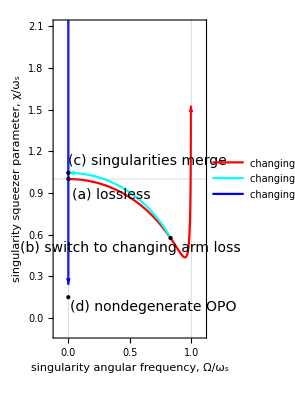

```mathematica
(*plotting pole-defined threshold values*)
Clear[plotPoleThresholdA,plotPoleThresholdC]
(*plotPoleThresholdA[Tlb0_,Tlc0_,PlotRange0_:Automatic,isPlotLabel_:True,PlotStyle0_:Automatic]:=
ParametricPlot[
Evaluate[Table[{Ω/ωs,χ/ωs}/.poleSol[[j]]/.{γa->γaFn[Tla0],γbtot->γbtotFn[Tlb0],γc->γcFn[Tlc0]},{j,1,Length[poleSol]}]],
{Tla0,0,1},Frame->True,FrameTicksStyle->Directive[14],FrameLabel->{{Style["singularity squeezer parameter, χ/ω_s",14],},{Style["singularity angular frequency, Ω/ω_s",14],If[isPlotLabel,StringForm["nondegenerate internal squeezing\nparameters of LIGO Voyager\nthreshold as singularities of anti-sqz'd quadrature\nas a function of T_(l, a)∈(0,1)\nT_(l, b)=``, T_(l, c)=``",Tlb0,Tlc0]]}},AspectRatio->Full,GridLines->{{0,1},{1}},PerformanceGoal->"Quality",PlotRange->PlotRange0,PlotStyle->PlotStyle0,PlotLegends->LineLegend[Range[Length[poleSol]],LabelStyle->Directive[14],LegendLabel->Style["changing T_(l, a)∈(0,1)\nindex of singularity in solution set",14]]]/.Line[x__]:>Sequence[Arrowheads->{{0.05,0.999999}},Arrow[x]]*)
plotPoleThresholdA2[Tlb0_,Tlc0_,PlotRange0_:Automatic,isPlotLabel_:True,PlotStyle0_:{Blue,Cyan}]:=
ParametricPlot[
Evaluate[Table[{Ω/ωs,χ/ωs}/.poleSol[[j]]/.{γa->γaFn[Tla0],γbtot->γbtotFn[Tlb0],γc->γcFn[Tlc0]},{j,1,Length[poleSol]}]],
{Tla0,0,1},Frame->True,FrameTicksStyle->Directive[14],FrameLabel->{{Style["singularity squeezer parameter, χ/ω_s",14],},{Style["singularity angular frequency, Ω/ω_s",14],If[isPlotLabel,StringForm["nondegenerate internal squeezing\nparameters of LIGO Voyager\nthreshold as singularities of anti-sqz'd quadrature\nas a function of T_(l, a)∈(0,1)\nT_(l, b)=``, T_(l, c)=``",Tlb0,Tlc0]]}},AspectRatio->Full,GridLines->{{0,1},{1}},PerformanceGoal->"Quality",PlotRange->PlotRange0,PlotStyle->PlotStyle0,PlotLegends->LineLegend[Reverse[PlotStyle0],{"changing T_(l, a)∈(0,1) with T_(l, b)=0, T_(l, c)=0.1\nfirst singularity","changing T_(l, a)∈(0,1) with T_(l, b)=0, T_(l, c)=0.1\nsecond singularity"},LabelStyle->Directive[14]]]/.Line[x__]:>Sequence[Arrowheads->{{0.05,0.999999},{0.05,0.5}},Arrow[x]]
(*plotPoleThresholdC[Tla0_,Tlb0_,PlotRange0_:Automatic,isPlotLabel_:True,PlotStyle0_:Automatic]:=
ParametricPlot[
Evaluate[Table[{Ω/ωs,χ/ωs}/.poleSol[[j]]/.{γa->γaFn[Tla0],γbtot->γbtotFn[Tlb0],γc->γcFn[Tlc0]},{j,1,Length[poleSol]}]],
{Tlc0,0,1},Frame->True,FrameTicksStyle->Directive[14],FrameLabel->{{Style["singularity squeezer parameter, χ/ω_s",14],},{Style["singularity angular frequency, Ω/ω_s",14],If[isPlotLabel,StringForm["nondegenerate internal squeezing\nparameters of LIGO Voyager\nthreshold as singularities of anti-sqz'd quadrature\nas a function of T_(l, c)∈(0,1)\nT_(l, a)=``, T_(l, b)=``",Tla0,Tlb0]]}},AspectRatio->Full,GridLines->{{0,1},{1}},PerformanceGoal->"Quality",PlotRange->PlotRange0,PlotStyle->PlotStyle0,PlotLegends->LineLegend[Range[Length[poleSol]],LabelStyle->Directive[14],LegendLabel->Directive["changing T_(l, c)∈(0,1)\nindex of singularity in solution set",14]]]/.Line[x__]:>Sequence[Arrowheads->{{0.05,0.999999}},Arrow[x]]*)
plotPoleThresholdC2[Tla0_,Tlb0_,PlotRange0_:Automatic,isPlotLabel_:True,PlotStyle0_:Automatic]:=
ParametricPlot[
Evaluate[{Ω/ωs,χ/ωs}/.poleSol[[2]]/.{γa->γaFn[Tla0],γbtot->γbtotFn[Tlb0],γc->γcFn[Tlc0]}],
{Tlc0,0,1},Frame->True,FrameTicksStyle->Directive[14],FrameLabel->{{Style["singularity squeezer parameter, χ/ω_s",14],},{Style["singularity angular frequency, Ω/ω_s",14],If[isPlotLabel,StringForm["nondegenerate internal squeezing\nparameters of LIGO Voyager\nthreshold as singularities of anti-sqz'd quadrature\nas a function of T_(l, c)∈(0,1)\nT_(l, a)=``, T_(l, b)=``",Tla0,Tlb0]]}},AspectRatio->Full,GridLines->{{0,1},{1}},PerformanceGoal->"Quality",PlotRange->PlotRange0,PlotStyle->PlotStyle0,PlotLegends->LineLegend[{"changing T_(l, c)∈(0,1) with T_(l, a)=T_(l, b)=0"},LabelStyle->Directive[14]]]/.Line[x__]:>Sequence[Arrowheads->{{0.05,0.999999},{0.05,0.3}},Arrow[x]]

(*colour function is the wrong way round for Tla plot? poles should collide at large γa?
--> have left out ColorFunction, to-do: figure out what was wrong*)
(*
plotPoleThresholdA[0.1,0.1]
plotPoleThresholdC[0,0,All]
*)

(*pole-definition combined plot: going from lossless sWLC to nOPO*)
Tlc1=0.1;
p1=plotPoleThresholdA2[0,0.1,{{0,1},{0,3}},False];
p2=plotPoleThresholdC2[0,0,{{0,1},{0,3}},False,{Red}];
Show[p2,p1,PlotRange->{{0-0.1,1+0.1},{0-0.1,2+0.1}},
Epilog->{
Black,PointSize[Large],Point[{0,1}],Text[Style["(a) lossless",14],Offset[{43,-15},{0,1}]],
Black,PointSize[Large],Point[{0,1/ωs Sqrt[γbtotFn[0]γcFn[Tlc1]]}],Text[Style["(d) nondegenerate OPO",14],Offset[{85,-10},{0,1/ωs Sqrt[γbtotFn[0]γcFn[Tlc1]]}]],
Black,PointSize[Large],Point[{1/ωs Sqrt[(γcFn[Tlc1] ωs^2)/(γbtotFn[0]+γcFn[Tlc1])],1/ωs Sqrt[γbtotFn[0](γcFn[Tlc1]+ωs^2/(γbtotFn[0]+γcFn[Tlc1]))]}],Text[Style["(b) switch to changing arm loss",14],Offset[{-40,-10},{1/ωs Sqrt[(γcFn[Tlc1] ωs^2)/(γbtotFn[0]+γcFn[Tlc1])],1/ωs Sqrt[γbtotFn[0](γcFn[Tlc1]+ωs^2/(γbtotFn[0]+γcFn[Tlc1]))]}]],Black,PointSize[Large],Point[{0,1/ωs √(γbtotFn[0] γcFn[Tlc1]+1/2 ωs (ωs+√(4 γcFn[Tlc1] (γbtotFn[0]+γcFn[Tlc1])+ωs^2)))}],Text[Style["(c) singularities merge",14],Offset[{79,12},{0,1/ωs √(γbtotFn[0] γcFn[Tlc1]+1/2 ωs (ωs+√(4 γcFn[Tlc1] (γbtotFn[0]+γcFn[Tlc1])+ωs^2)))}]]
}
]
Export[NotebookDirectory[]<>"nIS_threshold.pdf",%];
```

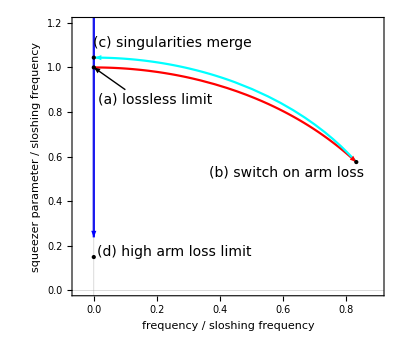

```mathematica
Clear[plotPoleThresholdA,plotPoleThresholdC]
plotPoleThresholdA2[Tlb0_,Tlc0_,PlotRange0_:Automatic,isPlotLabel_:True,PlotStyle0_:{Blue,Cyan}]:=
ParametricPlot[
Evaluate[Table[{Ω/ωs,χ/ωs}/.poleSol[[j]]/.{γa->γaFn[Tla0],γbtot->γbtotFn[Tlb0],γc->γcFn[Tlc0]},{j,1,Length[poleSol]}]],
{Tla0,0,1},Frame->True,FrameTicksStyle->Directive[14],FrameLabel->{{,},{,If[isPlotLabel,StringForm["nondegenerate internal squeezing\nparameters of LIGO Voyager\nthreshold as singularities of anti-sqz'd quadrature\nas a function of T_(l, a)∈(0,1)\nT_(l, b)=``, T_(l, c)=``",Tlb0,Tlc0]]}},AspectRatio->Full,GridLines->{{0},{}},PerformanceGoal->"Quality",PlotRange->PlotRange0,PlotStyle->PlotStyle0]/.Line[x__]:>Sequence[Arrowheads->{{0.05,0.999999},{0.05,0.5}},Arrow[x]]

TlcMax=0.1;
plotPoleThresholdC2[Tla0_,Tlb0_,PlotRange0_:Automatic,isPlotLabel_:True,PlotStyle0_:Automatic]:=
ParametricPlot[
Evaluate[{Ω/ωs,χ/ωs}/.poleSol[[2]]/.{γa->γaFn[Tla0],γbtot->γbtotFn[Tlb0],γc->γcFn[Tlc0]}],
{Tlc0,0,TlcMax},Frame->True,FrameTicksStyle->Directive[14],FrameLabel->{{Style["squeezer parameter / sloshing frequency",14],},{Style["frequency / sloshing frequency",14],}},AspectRatio->Full,GridLines->{{0},{0}},PerformanceGoal->"Quality",PlotRange->PlotRange0,PlotStyle->PlotStyle0]/.Line[x__]:>Sequence[Arrowheads->{{0.05,0.8},{0.05,0.3}},Arrow[x]]

(*pole-definition combined plot: going from lossless sWLC to nOPO*)
Tlc1=0.1;
p1=plotPoleThresholdA2[0,0.1,{{0,1},{0,3}},False];
p2=plotPoleThresholdC2[0,0,{{0,1},{0,3}},False,{Red}];
Show[p2,p1,ImageSize->{400,350},PlotRange->{{0-0.05,0.9},{0,1.2}},
Epilog->{
Black,PointSize[Large],Point[{0,1}],Text[Style["(a) lossless limit",14],Offset[{30,-10},{0.1,0.9}]],
Black,PointSize[Large],Point[{0,1/ωs Sqrt[γbtotFn[0]γcFn[Tlc1]]}],
Arrow[{{0.1,0.9},{0,1}}],Text[Style["(d) high arm loss limit",14],Offset[{80,5},{0,1/ωs Sqrt[γbtotFn[0]γcFn[Tlc1]]}]],
Black,PointSize[Large],Point[{1/ωs Sqrt[(γcFn[Tlc1] ωs^2)/(γbtotFn[0]+γcFn[Tlc1])],1/ωs Sqrt[γbtotFn[0](γcFn[Tlc1]+ωs^2/(γbtotFn[0]+γcFn[Tlc1]))]}],Text[Style["(b) switch on arm loss",14],Offset[{-70,-10},{1/ωs Sqrt[(γcFn[Tlc1] ωs^2)/(γbtotFn[0]+γcFn[Tlc1])],1/ωs Sqrt[γbtotFn[0](γcFn[Tlc1]+ωs^2/(γbtotFn[0]+γcFn[Tlc1]))]}]],Black,PointSize[Large],Point[{0,1/ωs √(γbtotFn[0] γcFn[Tlc1]+1/2 ωs (ωs+√(4 γcFn[Tlc1] (γbtotFn[0]+γcFn[Tlc1])+ωs^2)))}],Text[Style["(c) singularities merge",14],Offset[{79,15},{0,1/ωs √(γbtotFn[0] γcFn[Tlc1]+1/2 ωs (ωs+√(4 γcFn[Tlc1] (γbtotFn[0]+γcFn[Tlc1])+ωs^2)))}]]}]
Export[NotebookDirectory[]<>"talk_nIS_threshold.pdf",%];
```

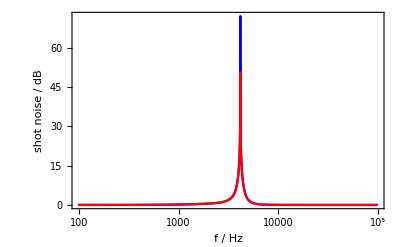

```mathematica
(*plotting pole: watch out for @ versus @@ (which unpacks)
--> increasing plotPoints samples the pole more*)
Block[{Tla0=0,Tlb0=0,Tlc0=0.1,Rpd=0,
plotter=
LogLinearPlot[20 1/2 Log10[Sx1@@{2π f,χ}/.poleSol[[2]]/.{γa->γaFn[Tla0],γbtot->γbtotFn[Tlb0],γc->γcFn[Tlc0]}],{f,0,10^5},PlotRange->All,PlotPoints->#1,ClippingStyle->Red,PlotStyle->#2,Frame->True,FrameLabel->{{"shot noise / dB",},{"f / Hz",}}]&},
Show[plotter[1000,Blue],plotter[100,Red]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

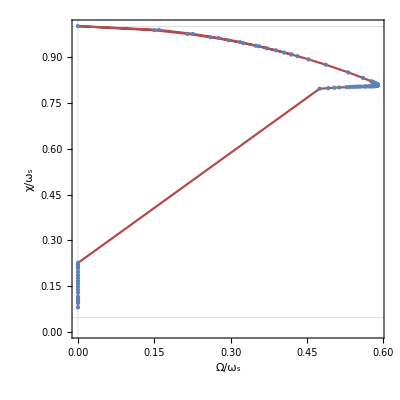

```mathematica
(*plotting gradient method to maximise anti-squeezed quadrature
--> how this differs from the pole find I do not know, nor why the numerics differ*)

(*plotting one solution -- using Solve on Gradient==0 rather than native optimisation*)
(*should be using NSolve for numerical solutions, Solve could be inaccurate?*)
(*to-do: why doesn't finding the sol separately instead of for each point not work?
e.g. sol=Solve[{(GradSx[Ω,χ]/.{γbtot->γR,γa->0,Rpd->0})=={0,0},Ω≥0,χ≥0,γc>0},{Ω,χ}];
ParametricPlot[Block[{γc=γcFn[Tlc]},{Ω/ωs,χ/ωs}/.sol[[-1]]],*)
Tlb0=0;
γbtot=γbtotFn[Tlb0];
Tlc0=1. 10^-2;
γc=γcFn[Tlc0];
ParametricPlot[Block[{γa=γaFn[Tla]},{Ω/ωs,χ/ωs}/.Solve[{(GradSx[Ω,χ]/.{Rpd->0})=={0,0},Ω≥0,χ≥0},{Ω,χ}][[-1]]],
{Tla,0,1},PerformanceGoal->"Speed",AspectRatio->1,PlotRange->{Automatic,{0,Automatic}},Frame->True,FrameLabel->{{"χ/ω_s",},{"Ω/ω_s",StringForm["nondegenerate internal squeezing\nparameters of LIGO Voyager\nthreshold points, i.e. extrema of S_x(Ω,χ) (shot noise)\nas a function of T_(l, a)∈(0,1)\nT_(l, b)=``, T_(l, c)=``, R_PD=``",Tlb0,Tlc0,0]}},GridLines->{{0,1},{1,1/ωs(γbtot γc)^(1/2)}},ColorFunction->"Rainbow",Mesh->All]
Clear[γbtot,γc]
(*plot goes in wrong direction, has a strange hook, and misses the DC pole until the end --> can see how this is related to the analytics but don't understand why reversed etc.*)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

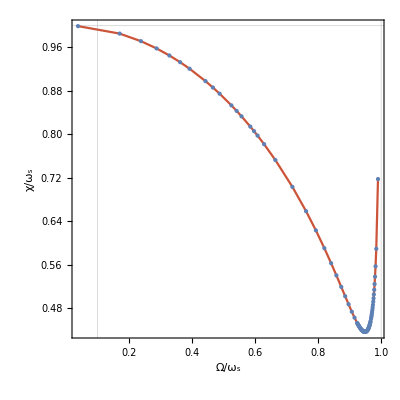

```mathematica
Clear[γbtot,γa]
ParametricPlot[Block[{γc=γaFn[Tlc]},{Ω/ωs,χ/ωs}/.Solve[{(GradSx[Ω,χ]/.{γbtot->γR,γa->0,Rpd->0})=={0,0},Ω≥0,χ≥0},{Ω,χ}][[-1]]],
{Tlc,0,1},PerformanceGoal->"Speed",AspectRatio->1,PlotRange->All,Frame->True,FrameLabel->{{"χ/ω_s",},{"Ω/ω_s",StringForm["nondegenerate internal squeezing\nparameters of LIGO Voyager\nthreshold points, i.e. extrema of S_x(Ω,χ) (shot noise)\nas a function of T_(l, c)∈(0,1)\nT_(l, a)=0, T_(l, b)=``, R_PD=``",0,0]}},GridLines->{{0,0.1,1},{1}},ColorFunction->"Rainbow",Mesh->All]
(*plot looks pretty similar to analytics -- nice!*)
```

```mathematica
Tla0=0;
γa=γaFn[Tla0];
Tlc0=1. 10^-2;
γc=γcFn[Tlc0];
ParametricPlot[Block[{γbtot=γbtotFn[Tlb]},{Ω/ωs,χ/ωs}/.Solve[{(GradSx[Ω,χ]/.{Rpd->0})=={0,0},Ω≥0,χ≥0},{Ω,χ}][[-1]]],
{Tlb,0,1},PerformanceGoal->"Speed",AspectRatio->1,PlotRange->{Automatic,{0,Automatic}},Frame->True,FrameLabel->{{"χ/ω_s",},{"Ω/ω_s",StringForm["nondegenerate internal squeezing\nparameters of LIGO Voyager\nthreshold points, i.e. extrema of S_x(Ω,χ) (shot noise)\nas a function of T_(l, b)∈(0,1)\nT_(l, a)=``, T_(l, c)=``, R_PD=``",Tla0,Tlc0,0]}},GridLines->{{0,1},{1}},ColorFunction->"Rainbow",Mesh->All]
Clear[γa,γc]
(*haven't plotted analytics against Tlb -- could do to compare*)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

$Aborted

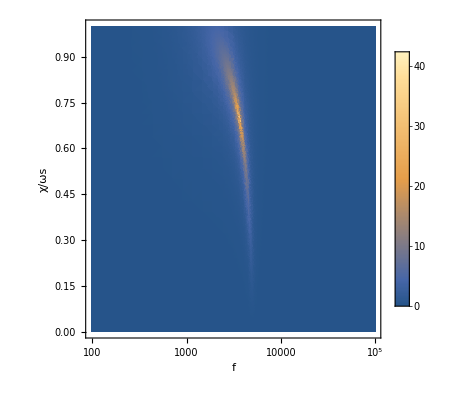

NMaximize::nrnum: The function value -141.919-13.6438 ⅈ is not a real number at {f,χRatio} = {3610.24,0.699671}.

{144.929,{f→3610.24,χRatio→0.699671}}

{10.6644,{f→2843.04}}

{1.,{f→1.54761}}

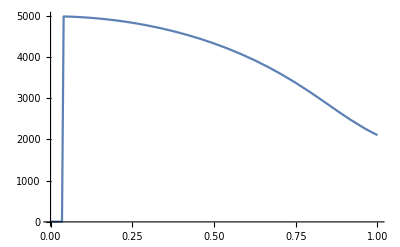

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{1.,{Ω→2.582503249,χ→1.075682708}}

```mathematica
γa=γaFn[0];
γbtot=γbtotFn[0];
γc=γcFn[0.05];
Rpd=0;
DensityPlot[20Log10[Sx1[2π f,χRatio ωs]^(1/2)],{f,0,10^5},{χRatio,0,1},PlotLegends->Automatic,Frame->True,FrameLabel->{{"χ/ωs",},{"f",}},ScalingFunctions->{"Log",None},PlotRange->All,MaxRecursion->5]
NMaximize[{20Log10[Sx1[2π f,χRatio ωs]^(1/2)],10^5≥f≥0,1≥χRatio≥0},{f,χRatio}]

NMaximize[{Sx1[2π f,0.85ωs],f≥0},f]
FindMaximum[{Sx1[2π f,0.85ωs],f≥0},f]
Plot[f/.NMaximize[{Sx1[2π f,ratio ωs],f≥0},f][[2]],{ratio,0,1},PerformanceGoal->"Speed"]
γa=0;
γbtot=γR;
γc=γcFn[0.01];
Rpd=0;
NMaximize[{Sx1[Ω,χ],Ω≥0,χ≥0},{Ω,χ},WorkingPrecision->10]
(*
FindMaximum[{Sx1[2π f,0.01 ωs],f≥0},f]
Plot[Sx1[2π f,0.01 ωs],{f,0,10^4},PlotRange->All]
*)
Clear[γa,γbtot,γc,Rpd]

(*
Clear[γc]
sol=Solve[{(GradSx[Ω,χ]/.{γbtot->γR,γa->0,Rpd->0})=={0,0},Ω≥0,χ≥0,γc>0},{Ω,χ}];
pointSol=Select[sol,(Length[#]==2)&];
*)

(*two peaks?*)
Clear[γa]
γa=γaFn[0.5];
Tlb0=0;
γbtot=γbtotFn[Tlb0];
Tlc0=1. 10^-2;
γc=γcFn[Tlc0];
NSolve[{(GradSx[Ω,χ]/.{Rpd->0})=={0,0},Ω≥0,χ≥0},{Ω,χ},Reals]
Clear[γa,γbtot,γc,Rpd]
```